A SHORT-PERIOD HELICAL WIGGLE AS AN IMPROVED SOURCE OF SYNCHROTRON RADIATION

Brian M. Kincaid

II. HELICAL MAGNETIC FIELDS AND SYNCHROTRON RADIATION FROM A HELICAL ELECTRON ORBIT

B_⊥=(8 π I)/(10 λ_0)[(2 π a)/λ_0 K_0((2 π a)/λ_0) + K_1((2 π a)/λ_0)]											(1)

```mathematica
Bprp=Function[{Ic,λ0,a},(8 π Ic)/(10 λ0)((2 π a)/λ0 BesselK[0,(2 π a)/λ0] + BesselK[1,(2 π a)/λ0] )  ];
```

General::ivar: 1 is not a valid variable.

1/5 π (1/2 π BesselK[0,π/2]+BesselK[1,π/2])

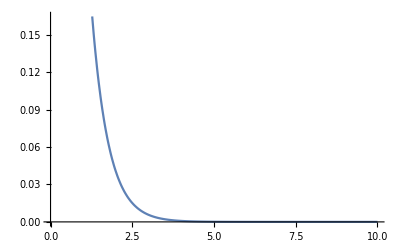

```mathematica
ans=Series[Bprp[Ic,λ0,a],{a,0,2}];
ans=Normal[ans]
Plot[Bprp[1,3,x],{x,0,10}]
```

B_⊥ is not exactly a decreasing exponential, as can be seen in the Taylor expansion, but has an assymptotic qualitative resemblance.

```mathematica
Clear[c,q,m,ρ ,γ, β, βs, B,K,ω0,b,Nn,a,λ0,Ic]
```

```mathematica
c=1; (*speed of light*)
q=1;(*charge*)
m=1;(*mass*)
a=1; (*radius of helix*)
λ0=4; (*magnet period*)
Ic=1; (*Current in amps*)
B=Bprp[Ic,λ0,a] (*Magnetic field*)
Nn=100;
ρ =γ β m c^2 / (q B)
b=(λ0/(2 π ρ))^2 ρ (1-(λ0/(2 π ρ)))^-0.5
γ=300
β=Sqrt[1-1/(γ*γ)]
βs=β(1-(K/γ)^2)^0.5
ω0=(2 π βs c)/λ0
```

1/5 π (1/2 π BesselK[0,π/2]+BesselK[1,π/2])

(5 β γ)/(π (1/2 π BesselK[0,π/2]+BesselK[1,π/2]))

(4 (1/2 π BesselK[0,π/2]+BesselK[1,π/2]))/(5 π β γ (1-(2 (1/2 π BesselK[0,π/2]+BesselK[1,π/2]))/(5 β γ))^0.5)

300

(√89999)/300

1/300 √89999 (1-K^2/90000)^0.5

1/600 √89999 (1-K^2/90000)^0.5 π

```mathematica
vecN=Function[θ,{0,Sin[θ],Cos[θ]}]
vecR=Function[t,{b Cos[ω0 t], a Sin[ω0 t], βs c t}]
vecβ=Function[t,D[vecR,t]/c]
```

Function[θ,{0,Sin[θ],Cos[θ]}]

Function[t,{b Cos[ω0 t],a Sin[ω0 t],βs c t}]

Function[t,(∂_t vecR)/c]

```mathematica
vecR[t]
Norm[vecR[t]]
```

{0.000473195 Cos[1/600 √89999 (1-K^2/90000)^0.5 π t],Sin[1/600 √89999 (1-K^2/90000)^0.5 π t],1/300 √89999 (1-K^2/90000)^0.5 t}

√((89999 Abs[(1-K^2/90000)^0.5 t]^2)/90000+2.23914×10^-7 Abs[Cos[1/600 √89999 (1-K^2/90000)^0.5 π t]]^2+Abs[Sin[1/600 √89999 (1-K^2/90000)^0.5 π t]]^2)

```mathematica
vecT=Table[t,{t,-10,10,0.02}];
```

```mathematica
vecX=vecR[vecT][[1]]/.K->1;
vecY=vecR[vecT][[2]]/.K->1;
vecZ=vecR[vecT][[3]]/.K->1;
```

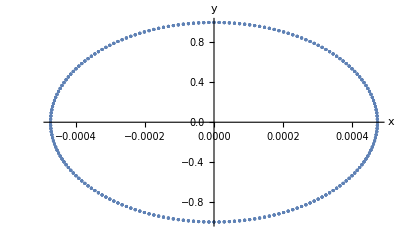

```mathematica
ListPlot[Transpose[{vecX,vecY}],AxesLabel->{x,y}]
```

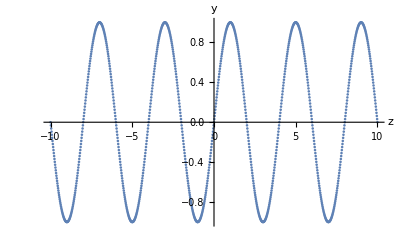

```mathematica
ListPlot[Transpose[{vecZ,vecY}],AxesLabel->{z,y}]
```

III. COMPARISON WITH BENDING MAGNET AND NORMAL WIGGLER

```mathematica
Clear[c,hbar,r,ρ,Ec,γ,m,q,B,λ0,K,En,β]
```

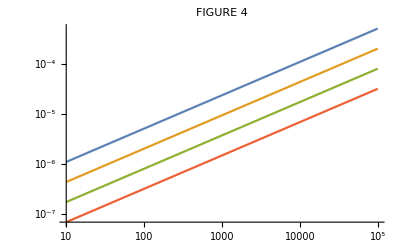

```mathematica
Clear[c,hbar,r,ρ,Ec,γ,m,q,B,λ0,K,En,β]
c=1; (*speed of light*)
q=1;(*1.6*10^-19 charge*)
m0=511*1000;(*mass*)
m=1;(* 511*1000 mass*)
hbar=1; (*Plack constant*)
λ0=0.01; (*magnet period*)

K=1;
γ=Sqrt[1+(En/(m c^2))^2];
β=Sqrt[1-1/(γ*γ)];

ρ =(γ β λ0 c)/(2 π K);
Ec=1.5 (hbar c / ρ) γ^3;
r=hν/Ec;
dIdΩ=Function[hν,3/(4 π^2)r^2 BesselK[2/3,r/2]^2];

LogLogPlot[
{dIdΩ[hν]/.En->(0.5*10^9)/m0,dIdΩ[hν]/.En->(1.0*10^9)/m0,dIdΩ[hν]/.En->(2.0*10^9)/m0,dIdΩ[hν]/.En->(4.0*10^9)/m0}
,{hν,10,10^5},PlotLabel->"FIGURE 4"]
```

{0.5,0.75,1,1.25,1.5,2}

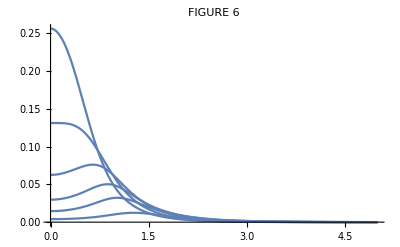

```mathematica
(*Figure 6*)
Clear[c,hbar,r,ρ,Ec,γ,m,q,B,λ0,Kk,En,β, n,γθ]
xn=Function[{Kk,n,γθ},(2 Kk n γθ)/(1+Kk^2+(γθ)^2)];
dWdΩ=Function[Kk,1/((1+Kk^2+(γθ)^2)^3)Sum[n^2*(  (D[BesselJ[n,y],y]/.y->xn[Kk,n,γθ])^2 + (γθ/Kk-n/xn[Kk,n,γθ])^2 BesselJ[n,xn[Kk,n,γθ]]^2  ),{n,1,10}]];
vecKk={0.5,0.75,1,1.25,1.5,2}
Plot[
{dWdΩ[Kk]/.Kk->vecKk},{γθ,0,5},PlotRange->All,PlotLegends->Automatic,PlotLabel->"FIGURE 6"]
```